```mathematica
NSolve[x Exp[-x]==0.25,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.357403},{x→2.15329}}

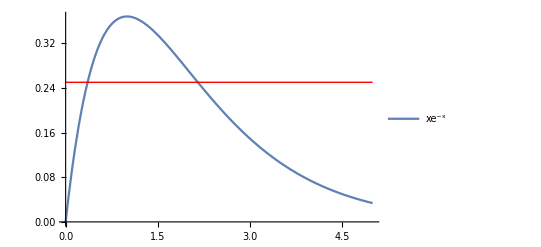

```mathematica
Show[Plot[x Exp[-x],{x,0,5},PlotLegends->{"xe^-x"}],Graphics[{Red,Line[{{0,0.25},{5,0.25}}]}],AxesStyle->15]
```

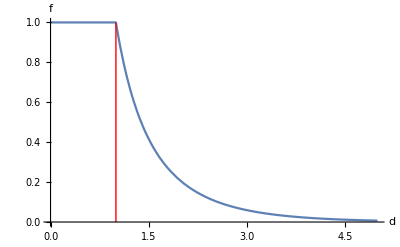

```mathematica
Show[Plot[-LambertW[-x Exp[-x]]/x,{x,0,5},AxesStyle->Directive[{Black,15}],AxesLabel->{"d","f"}],Graphics[{Red,Line[{{1,0},{1,1}}]}]]
```